```mathematica
Unprotect[AR,AS,CS,R];
Remove[AR, AS, CS,R];
$Assumptions=Subscript[θ, a]∈ Reals &&Subscript[ϕ, a]∈Reals&&ϕ∈Reals;
```

```mathematica
(*AR[θ_]:={{Cos[θ/2],0,ⅈ*Sin[θ/2],0},{0,Cos[θ/2],0,ⅈ*Sin[θ/2]},{ⅈ*Sin[θ/2],0,Cos[θ/2],0},{0,ⅈ*Sin[θ/2],0,Cos[θ/2]}}
AS[ϕ_]:={{Cos[ϕ/2],ⅈ*Sin[ϕ/2],0,0},{ⅈ*Sin[ϕ/2],Cos[ϕ/2],0,0},{0,0,Cos[ϕ/2],ⅈ*Sin[ϕ/2]},{0,0,ⅈ*Sin[ϕ/2],Cos[ϕ/2]}}*)
```

```mathematica
AR[θ_]:={{-Cos[θ],0,-Sin[θ],0},{0,-Cos[θ],0,-Sin[θ]},{-Sin[θ],0,Cos[θ],0},{0,-Sin[θ],0,Cos[θ]}}
AS[ϕ_]:={{Cos[ϕ/2],ⅈ*Sin[ϕ/2],0,0},{ⅈ*Sin[ϕ/2],Cos[ϕ/2],0,0},{0,0,Cos[ϕ/2],ⅈ*Sin[ϕ/2]},{0,0,ⅈ*Sin[ϕ/2],Cos[ϕ/2]}}
```

```mathematica
(*CS[G_]:=(G[[1,1]]-G[[2,2]]-G[[3,3]]+G[[4,4]])/(G[[1,1]]+G[[2,2]]+G[[3,3]]+G[[4,4]])*)
```

```mathematica
CS[G_]:=(G[[1,1]]-G[[2,2]]-G[[3,3]]+G[[4,4]])/(G[[1,1]]+G[[2,2]]+G[[3,3]]+G[[4,4]])
```

```mathematica
Subscript[G, in]=1/2{{Cos[ϕ/2]^2,ⅈ*Cos[ϕ/2]Sin[ϕ/2],Cos[ϕ/2],0},{-ⅈ*Cos[ϕ/2]Sin[ϕ/2],Sin[ϕ/2]^2,-ⅈ*Sin[ϕ/2],0},{Cos[ϕ/2],ⅈ*Sin[ϕ/2],1,0},{0,0,0,0}};
```

```mathematica
MatrixForm[AR[Subscript[θ, a]]]
MatrixForm[AS[Subscript[ϕ, a]]]
MatrixForm[Subscript[G, in]]
```

(-Cos[θ_a] | 0 | -Sin[θ_a] | 0
0 | -Cos[θ_a] | 0 | -Sin[θ_a]
-Sin[θ_a] | 0 | Cos[θ_a] | 0
0 | -Sin[θ_a] | 0 | Cos[θ_a])

(Cos[ϕ_a/2] | ⅈ Sin[ϕ_a/2] | 0 | 0
ⅈ Sin[ϕ_a/2] | Cos[ϕ_a/2] | 0 | 0
0 | 0 | Cos[ϕ_a/2] | ⅈ Sin[ϕ_a/2]
0 | 0 | ⅈ Sin[ϕ_a/2] | Cos[ϕ_a/2])

(1/2 Cos[ϕ/2]^2 | 1/2 ⅈ Cos[ϕ/2] Sin[ϕ/2] | 1/2 Cos[ϕ/2] | 0
-1/2 ⅈ Cos[ϕ/2] Sin[ϕ/2] | 1/2 Sin[ϕ/2]^2 | -1/2 ⅈ Sin[ϕ/2] | 0
1/2 Cos[ϕ/2] | 1/2 ⅈ Sin[ϕ/2] | 1/2 | 0
0 | 0 | 0 | 0)

```mathematica
Subscript[G, out]=Refine[Conjugate[AS[Subscript[ϕ, a]]].Conjugate[AR[Subscript[θ, a]]].Subscript[G, in].Transpose[AR[Subscript[θ, a]]].Transpose[AS[Subscript[ϕ, a]]],{Element[Subscript[θ, a],Reals],Element[Subscript[ϕ, a],Reals],Element[ϕ,Reals]}];
```

```mathematica
MatrixForm[Simplify[Subscript[G, out]]]
```

(1/2 (Cos[ϕ/2] Cos[θ_a] Cos[ϕ_a/2]+Cos[ϕ_a/2] Sin[θ_a]-Cos[θ_a] Sin[ϕ/2] Sin[ϕ_a/2])^2 | 1/16 ⅈ (2 Cos[ϕ/2-2 θ_a+ϕ_a]-2 Cos[ϕ/2+2 θ_a+ϕ_a]+Sin[2 θ_a-ϕ_a]+2 Sin[ϕ_a]+2 Sin[ϕ+ϕ_a]+Sin[ϕ-2 θ_a+ϕ_a]-Sin[2 θ_a+ϕ_a]+Sin[ϕ+2 θ_a+ϕ_a]) | 1/16 (-2 Cos[ϕ/2-2 θ_a]-2 Cos[ϕ/2+2 θ_a]-2 Cos[ϕ/2-2 θ_a+ϕ_a]-2 Cos[ϕ/2+2 θ_a+ϕ_a]-Sin[2 θ_a-ϕ_a]-Sin[ϕ-2 θ_a+ϕ_a]-Sin[2 θ_a+ϕ_a]+Sin[ϕ+2 θ_a+ϕ_a]) | -1/16 ⅈ (Cos[2 θ_a-ϕ_a]-Cos[ϕ-2 θ_a+ϕ_a]-Cos[2 θ_a+ϕ_a]+Cos[ϕ+2 θ_a+ϕ_a]-4 Sin[ϕ/2]+2 Sin[ϕ/2-2 θ_a+ϕ_a]+2 Sin[ϕ/2+2 θ_a+ϕ_a])
-1/16 ⅈ (2 Cos[ϕ/2-2 θ_a+ϕ_a]-2 Cos[ϕ/2+2 θ_a+ϕ_a]+Sin[2 θ_a-ϕ_a]+2 Sin[ϕ_a]+2 Sin[ϕ+ϕ_a]+Sin[ϕ-2 θ_a+ϕ_a]-Sin[2 θ_a+ϕ_a]+Sin[ϕ+2 θ_a+ϕ_a]) | 1/2 (Sin[θ_a] Sin[ϕ_a/2]+Cos[θ_a] Sin[1/2 (ϕ+ϕ_a)])^2 | 1/16 ⅈ (Cos[2 θ_a-ϕ_a]-Cos[ϕ-2 θ_a+ϕ_a]-Cos[2 θ_a+ϕ_a]+Cos[ϕ+2 θ_a+ϕ_a]+4 Sin[ϕ/2]+2 Sin[ϕ/2-2 θ_a+ϕ_a]+2 Sin[ϕ/2+2 θ_a+ϕ_a]) | 1/16 (-2 Cos[ϕ/2-2 θ_a]-2 Cos[ϕ/2+2 θ_a]+2 Cos[ϕ/2-2 θ_a+ϕ_a]+2 Cos[ϕ/2+2 θ_a+ϕ_a]+Sin[2 θ_a-ϕ_a]+Sin[ϕ-2 θ_a+ϕ_a]+Sin[2 θ_a+ϕ_a]-Sin[ϕ+2 θ_a+ϕ_a])
1/16 (-2 Cos[ϕ/2-2 θ_a]-2 Cos[ϕ/2+2 θ_a]-2 Cos[ϕ/2-2 θ_a+ϕ_a]-2 Cos[ϕ/2+2 θ_a+ϕ_a]-Sin[2 θ_a-ϕ_a]-Sin[ϕ-2 θ_a+ϕ_a]-Sin[2 θ_a+ϕ_a]+Sin[ϕ+2 θ_a+ϕ_a]) | -1/16 ⅈ (Cos[2 θ_a-ϕ_a]-Cos[ϕ-2 θ_a+ϕ_a]-Cos[2 θ_a+ϕ_a]+Cos[ϕ+2 θ_a+ϕ_a]+4 Sin[ϕ/2]+2 Sin[ϕ/2-2 θ_a+ϕ_a]+2 Sin[ϕ/2+2 θ_a+ϕ_a]) | 1/2 (Cos[θ_a] Cos[ϕ_a/2]-Cos[1/2 (ϕ+ϕ_a)] Sin[θ_a])^2 | -1/16 ⅈ (2 Cos[ϕ/2-2 θ_a+ϕ_a]-2 Cos[ϕ/2+2 θ_a+ϕ_a]+Sin[2 θ_a-ϕ_a]-2 Sin[ϕ_a]-2 Sin[ϕ+ϕ_a]+Sin[ϕ-2 θ_a+ϕ_a]-Sin[2 θ_a+ϕ_a]+Sin[ϕ+2 θ_a+ϕ_a])
1/16 ⅈ (Cos[2 θ_a-ϕ_a]-Cos[ϕ-2 θ_a+ϕ_a]-Cos[2 θ_a+ϕ_a]+Cos[ϕ+2 θ_a+ϕ_a]-4 Sin[ϕ/2]+2 Sin[ϕ/2-2 θ_a+ϕ_a]+2 Sin[ϕ/2+2 θ_a+ϕ_a]) | 1/16 (-2 Cos[ϕ/2-2 θ_a]-2 Cos[ϕ/2+2 θ_a]+2 Cos[ϕ/2-2 θ_a+ϕ_a]+2 Cos[ϕ/2+2 θ_a+ϕ_a]+Sin[2 θ_a-ϕ_a]+Sin[ϕ-2 θ_a+ϕ_a]+Sin[2 θ_a+ϕ_a]-Sin[ϕ+2 θ_a+ϕ_a]) | 1/16 ⅈ (2 Cos[ϕ/2-2 θ_a+ϕ_a]-2 Cos[ϕ/2+2 θ_a+ϕ_a]+Sin[2 θ_a-ϕ_a]-2 Sin[ϕ_a]-2 Sin[ϕ+ϕ_a]+Sin[ϕ-2 θ_a+ϕ_a]-Sin[2 θ_a+ϕ_a]+Sin[ϕ+2 θ_a+ϕ_a]) | 1/2 (Cos[ϕ_a/2] Sin[ϕ/2] Sin[θ_a]+(-Cos[θ_a]+Cos[ϕ/2] Sin[θ_a]) Sin[ϕ_a/2])^2)

```mathematica
Simplify[CS[Subscript[G, out]]]
```

1/4 (-Cos[2 θ_a-ϕ_a]+Cos[ϕ-2 θ_a+ϕ_a]-Cos[2 θ_a+ϕ_a]+Cos[ϕ+2 θ_a+ϕ_a]-2 Sin[ϕ/2-2 θ_a+ϕ_a]+2 Sin[ϕ/2+2 θ_a+ϕ_a])

### G_pol and G_par

```mathematica
Subscript[G, pol]={{Subscript[G, in][[1,1]]+Subscript[G, in][[2,2]],Subscript[G, in][[1,3]]+Subscript[G, in][[2,4]]},{Subscript[G, in][[3,1]]+Subscript[G, in][[4,2]],Subscript[G, in][[3,3]]+Subscript[G, in][[4,4]]}};
Subscript[G, par]={{Subscript[G, in][[1,1]]+Subscript[G, in][[3,3]],Subscript[G, in][[1,2]]+Subscript[G, in][[3,4]]},{Subscript[G, in][[2,1]]+Subscript[G, in][[4,3]],Subscript[G, in][[2,2]]+Subscript[G, in][[4,4]]}};
Simplify[MatrixForm[Subscript[G, pol]]]
Simplify[MatrixForm[Subscript[G, par]]]
```

(1/2 | 1/2 Cos[ϕ/2]
1/2 Cos[ϕ/2] | 1/2)

(1/4 (3+Cos[ϕ]) | 1/4 ⅈ Sin[ϕ]
-1/4 ⅈ Sin[ϕ] | 1/2 Sin[ϕ/2]^2)

### Part A

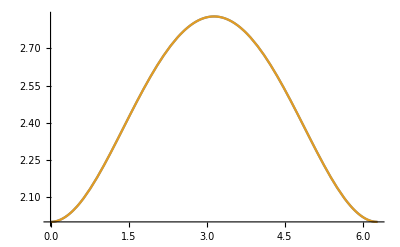

```mathematica
f[ta_,pa_,ϕ_]:=1.0*Sin[ta]*Cos[ϕ/2+pa]−0.5*Cos[ta]*Cos[pa]+0.5*Cos[ta]*Cos[ϕ+pa]
Plot[{MaxValue[Abs[f2[ta,pa,ϕ]+f2[ta,pb,ϕ]+f2[tb,pa,ϕ]-f2[tb,pb,ϕ]],{ta,pa,tb,pb}],2√(1+Sin[ϕ/2]^2)},{ϕ,0,2π}]
```

### Part B

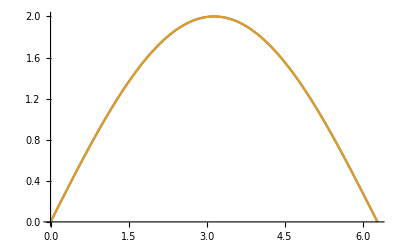

```mathematica
g[ta_,pa_,ϕ_]:=1/2*Cos[ta]*(Cos[pa+ϕ]-Cos[pa])
Plot[{MaxValue[Abs[g[ta,pa,ϕ]+g[ta,pb,ϕ]+g[tb,pa,ϕ]-g[tb,pb,ϕ]],{ta,pa,tb,pb}],2*Abs[Sin[ϕ/2]]},{ϕ,0,2π}]
```

### Part C

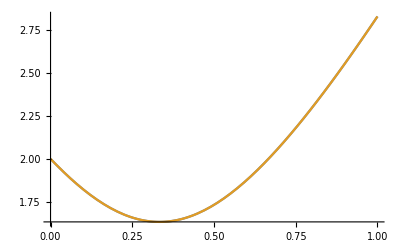

```mathematica
h[ta_,pa_,P_]:=(1-P)*Sin[ta]*Cos[pa]-P*Cos[ta-pa]
Plot[{MaxValue[Abs[h[ta,pa,P]+h[ta,pb,P]+h[tb,pa,P]-h[tb,pb,P]],{ta,pa,tb,pb}],2*√(1-2*P+3*P^2)},{P,0,1}]
```